Q8.13

```mathematica
U=3/2 n/β+n^2/V 2π
```

```mathematica
u[r_]:=u0((r0/r)^12-2(r0/r)^6)

FullSimplify[3/2 n/β+n^2/V 2π*Integrate[r^2 u[r]Exp[-u[r]β],{r,0,∞},Assumptions->{r0>0,u0>0,β>0}]]
```

1/(12 β)n (18-1/V ⅇ^((u0 β)/2) n π^2 r0^3 (3 u0 β BesselI[-1/4,(u0 β)/2]+(-1+3 u0 β) BesselI[1/4,(u0 β)/2]-u0 β (BesselI[3/4,(u0 β)/2]+BesselI[5/4,(u0 β)/2])))

```mathematica
β=1/(k T);
(*Taking all other constants to be equal to one*)
n=1;
u0=1;
k=1;
V=1;
r0=1;
U[T_]:=
1/(12 β)n (18-1/V ⅇ^((u0 β)/2) n π^2 r0^3 (3 u0 β BesselI[-1/4,(u0 β)/2]+(-1+3 u0 β) BesselI[1/4,(u0 β)/2]-u0 β (BesselI[3/4,(u0 β)/2]+BesselI[5/4,(u0 β)/2])))
```

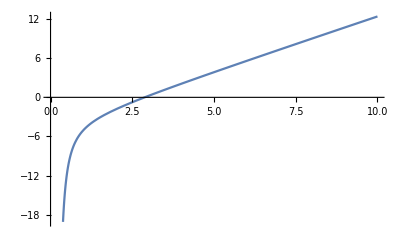

```mathematica
Plot[U[T],{T,0,10}]
```

```mathematica
U[T]
SpecificHeat[T_]=D[U[T],T]
```

1/12 T (18-ⅇ^(1/2/T) π^2 ((3 BesselI[-1/4,1/(2 T)])/T+(-1+3/T) BesselI[1/4,1/(2 T)]-(BesselI[3/4,1/(2 T)]+BesselI[5/4,1/(2 T)])/T))

1/12 (18-ⅇ^(1/2/T) π^2 ((3 BesselI[-1/4,1/(2 T)])/T+(-1+3/T) BesselI[1/4,1/(2 T)]-(BesselI[3/4,1/(2 T)]+BesselI[5/4,1/(2 T)])/T))+1/12 T ((ⅇ^(1/2/T) π^2 ((3 BesselI[-1/4,1/(2 T)])/T+(-1+3/T) BesselI[1/4,1/(2 T)]-(BesselI[3/4,1/(2 T)]+BesselI[5/4,1/(2 T)])/T))/(2 T^2)-ⅇ^(1/2/T) π^2 (-(3 BesselI[-1/4,1/(2 T)])/T^2-(3 BesselI[1/4,1/(2 T)])/T^2-(3 (BesselI[-5/4,1/(2 T)]+BesselI[3/4,1/(2 T)]))/(4 T^3)-((-1+3/T) (BesselI[-3/4,1/(2 T)]+BesselI[5/4,1/(2 T)]))/(4 T^2)+(BesselI[3/4,1/(2 T)]+BesselI[5/4,1/(2 T)])/T^2-(-(BesselI[-1/4,1/(2 T)]+BesselI[7/4,1/(2 T)])/(4 T^2)-(BesselI[1/4,1/(2 T)]+BesselI[9/4,1/(2 T)])/(4 T^2))/T))

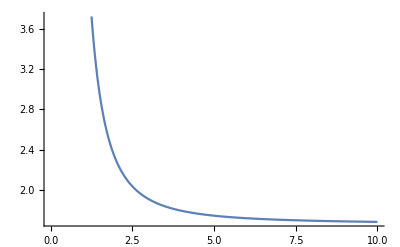

```mathematica
SpecificHeat[T];
Plot[SpecificHeat[T],{T,0,10}]
```